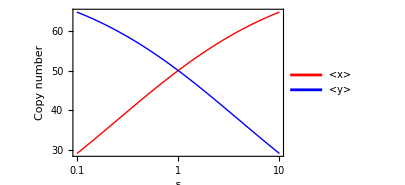
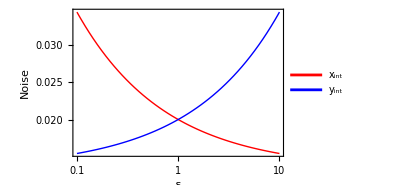
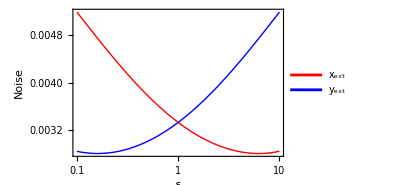
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*
This is part of the manuscript titled "Feedback-mediated circulation and persistence of stochastic fluctuations in gene
regulatory circuits" ;

Correspondence with the paper;

Please note ;
1. The four TNF motifs: Double positive feedback (++), Double negative feedback (--), Negative positive feedback (-+) and Positive negative feedback (+-);
2. αx and αy are production rates of X and Y;
3. βx and βy are degradation rates of X and Y;
4. fx=αx*gx, fy=αy*gy are the Hill functions with Hill coefficient=1;
5. xdot and ydot are the dynamical equations of X and Y;
6. xav=<x>, yav=<y> ;
7. fxyp = ∂fx/∂y and fyxp=∂fy/∂x are steady-state regulatory sensitivities;
8. G = H (feedback gain);
9. τxy and τyx are time-averaging factors;
9. δ is feedback strength;
10. The noise decomposition terms - intrinsic noise(xint,yint), extrinsic noise(xext,yext) and cyclic noise(xcy,ycy) are analytically derived from solving the Lyapunov equation to get the moments and then defining noise as dimensionless squared coefficient of variation;
11. xint and yint are the intrinsic noise terms of X and Y;
12. xext and yext are the extrinsic noise terms of X and Y;
13. The data is exported and plotted in another software 
====================================================================== 
*)

(* Double Positive Feedback *)

gx=y/(y+Kyx);gy=x/(x+Kxy); 

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

(*fixed points*)
xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fx=αx*gx;fy=αy*gy;

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;(*Derivative of functions fx, fy*)

(*time averaging factor*)
τyx=βy/(βx+βy);
τxy=βx/(βx+βy);

G=(fxyp*fyxp)/(βx*βy); (*Feedback gain*)

(*Noise Decomposition*)
xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p1=LogLinearPlot[{xav,yav},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Copy number"},ImageSize->300,PlotLegends->{"<x>","<y>"},PlotRange->All];
t1=Table[{δ,xav,yav},{δ,δi,δf,0.1}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
(*Export["D:\\nashitarahman\\DP1.dat",tp1,"FieldSeparators"->"    "];*)

p2=LogLinearPlot[{xint,yint},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_int","y_int"},PlotRange->All];
t2=Table[{δ,xint,yint},{δ,δi,δf,0.1}];
tp2=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t2];
(*Export["D:\\nashitarahman\\DP2int.dat",tp2,"FieldSeparators"->"    "];*)

p3=LogLinearPlot[{xext,yext},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_ext","y_ext"},PlotRange->All];
t3=Table[{δ,xext,yext},{δ,δi,δf,0.1}];
tp3=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t3];
(*Export["D:\\nashitarahman\\DP3ext.dat",tp3,"FieldSeparators"->"    "];*)

Grid[{{p1,p2,p3}}]

Quit[];
```

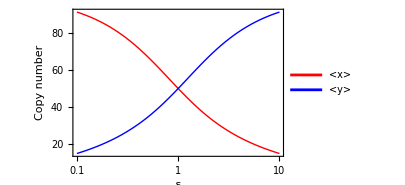
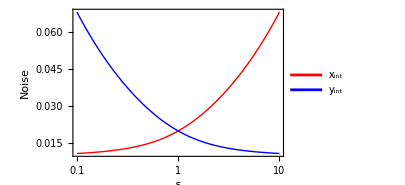
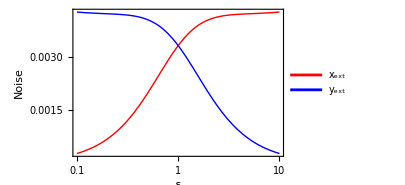
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Double negative feedback*)
gx=Kyx/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[1,1]];
yav=y/.sol[[1,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p1=LogLinearPlot[{xav,yav},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Copy number"},ImageSize->300,PlotLegends->{"<x>","<y>"},PlotRange->All];
t1=Table[{δ,xav,yav},{δ,δi,δf,0.1}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
(*Export["D:\\nashitarahman\\DN1.dat",tp1,"FieldSeparators"->"    "];*)

p2=LogLinearPlot[{xint,yint},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_int","y_int"},PlotRange->All];
t2=Table[{δ,xint,yint},{δ,δi,δf,0.1}];
tp2=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t2];
(*Export["D:\\nashitarahman\\DN2int.dat",tp2,"FieldSeparators"->"    "];*)

p3=LogLinearPlot[{xext,yext},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_ext","y_ext"},PlotRange->All];
t3=Table[{δ,xext,yext},{δ,δi,δf,0.1}];
tp3=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t3];
(*Export["D:\\nashitarahman\\DN3ext.dat",tp3,"FieldSeparators"->"    "];*)

Grid[{{p1,p2,p3}}]


Quit[];
```

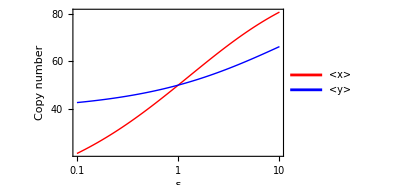
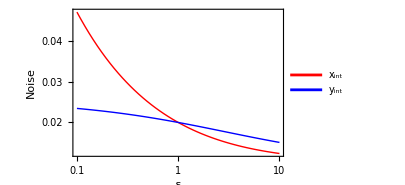
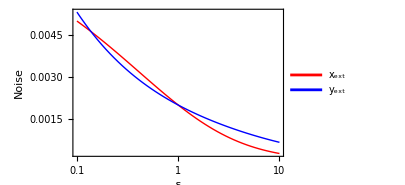
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Negative positive feedback*)

gx=y/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p1=LogLinearPlot[{xav,yav},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Copy number"},ImageSize->300,PlotLegends->{"<x>","<y>"},PlotRange->All];
t1=Table[{δ,xav,yav},{δ,δi,δf,0.1}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
(*Export["D:\\nashitarahman\\NP1.dat",tp1,"FieldSeparators"->"    "];*)

p2=LogLinearPlot[{xint,yint},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_int","y_int"},PlotRange->All];
t2=Table[{δ,xint,yint},{δ,δi,δf,0.01}];
tp2=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t2];
(*Export["D:\\nashitarahman\\NP2int.dat",tp2,"FieldSeparators"->"    "];*)

p3=LogLinearPlot[{xext,yext},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_ext","y_ext"},PlotRange->All];
t3=Table[{δ,xext,yext},{δ,δi,δf,0.01}];
tp3=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t3];
(*Export["D:\\nashitarahman\\NP3ext.dat",tp3,"FieldSeparators"->"    "];*)

Grid[{{p1,p2,p3}}]

Quit[];
```

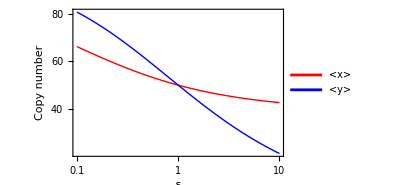
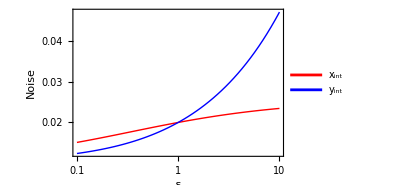
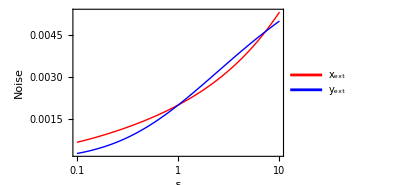
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Positive negative feedback*)
gx=Kyx/(y+Kyx);gy=x/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;

τyx=βy/(βx+βy);
τxy=βx/(βx+βy);
G=fxyp*fyxp/(βx*βy);

xint=1/xav;
xext=(fxyp^2 yav)/(βx(βx+βy)xav^2)*1/(1-G);
xcy =τyx* G/(1-G)*xint;
xtot=xint+xext+xcy;

yint=1/yav;
yext=(fyxp^2 xav)/(βy(βx+βy)yav^2)*1/(1-G);
ycy =τxy* G/(1-G)*yint;
ytot=yint+yext+ycy;

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

p1=LogLinearPlot[{xav,yav},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->Automatic,PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Copy number"},ImageSize->300,PlotLegends->{"<x>","<y>"},PlotRange->All];
t1=Table[{δ,xav,yav},{δ,δi,δf,0.01}];
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
(*Export["D:\\nashitarahman\\PN1.dat",tp1,"FieldSeparators"->"    "];*)

p2=LogLinearPlot[{xint,yint},{δ,δi,δf},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_int","y_int"},PlotRange->All];
t2=Table[{δ,xint,yint},{δ,δi,δf,0.01}];
tp2=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t2];
(*Export["D:\\nashitarahman\\PN2int.dat",tp2,"FieldSeparators"->"    "];*)

p3=LogLinearPlot[{xext,yext},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Noise"},ImageSize->300,PlotLegends->{"x_ext","y_ext"},PlotRange->All];
t3=Table[{δ,xext,yext},{δ,δi,δf,0.01}];
tp3=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t3];
(*Export["D:\\nashitarahman\\PN3ext.dat",tp3,"FieldSeparators"->"    "];*)

Grid[{{p1,p2,p3}}]

Quit[];
```